3.31818×10^-3

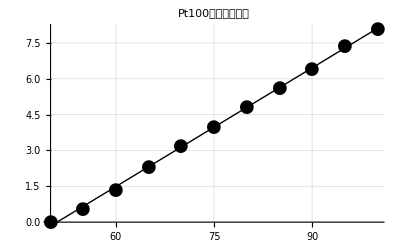

{{50,55,60,65,70,75,80,85,90,95,100},{0,0.56,1.35,2.31,3.2,4.,4.8,5.63,6.4,7.35,8.1}}

/Users/timfeirg/Documents/Medical-Sensor-Experiments/Exp11.xlsx

```mathematica
(*Exp11*)
temperature=Range[50,100,5];
volts={0,0.56,1.35,2.31,3.20,4.00,4.80,5.63,6.40,7.35,8.10};
coordinatesExp11=Transpose[{temperature,volts}];
linearFitExp11=LinearModelFit[coordinatesExp11,x,x];
PlotGraph=ListPlot[
coordinatesExp11,
PlotMarkers->{Automatic,18},
PlotStyle->Black,
GridLines->Automatic,
GridLinesStyle->Directive[Black,Dashed],
Frame->Automatic,
FrameLabel->{"T/°C","V/V"},
PlotLabel->"Pt100热电阻的特性",
BaseStyle->{FontWeight->"Bold",FontSize->18}
];
regressionExp11=Plot[Normal[linearFitExp11],
{x,Max[temperature],Min[temperature]},
PlotStyle->{Black,Thick}];
errorExp11=Max[Abs[linearFitExp11["FitResiduals"]]]/(Max[temperature]-Min[temperature])//ScientificForm
Show[PlotGraph,regressionExp11]
fullForm={temperature,volts}
Export["/Users/timfeirg/Documents/Medical-Sensor-Experiments/Exp11.xlsx",fullForm,"XLSX"]
```